```mathematica
(* ΑΡΜΟΝΙΚΟΣ ΤΑΛΑΝΤΩΤΗΣ *)
```

```mathematica
(* ΜΕ ΤΟΝ ΜΕΤΑΣΧΗΜΑΤΙΣΜΟ u(xi)=H(xi) Exp[-xi^2/2], Η ΕΞΙΣΩΣΗ ΤΟΥ Schrödinger(1.108)ΜΕΤΑΣΧΗΜΑΤΙΕΤΑΙ ΣΤΗΝ ΔΙΑΦΟΡΙΚΗ ΕΞΙΣΩΣΗ Hermite (1.110).
Η ΔΙΑΦΟΡΙΚΗ ΕΞΙΣΩΣΗ ΜΠΟΡΕΙ ΝΑ ΕΠΙΛΥΘΕΙ ΑΝΑΖΗΤΩΝΤΑΣ ΛΥΣΕΙΣ ΥΠΟ ΜΟΡΦΗ ΔΥΝΑΜΟΣΕΙΡΑΣ ΜΕ ΤΗ ΜΕΘΟΔΟ ΤΟΥ Frobenius.
ΕΜΕΙΣ ΘΑ ΤΗΝ ΛΥΣΟΥΜΕ ΜΕ ΤΗΝ ΕΝΤΟΛΗ NDSolve *)
```

```mathematica
Clear["Global`*"];
HOShrEq@psi_:=D[psi, {xi,2}]+(epsilon-xi^2)*psi (* ΣΧΕΣΗ 1.108 *)
u[xi_]=H[xi]*E^(-xi^2/2); (* ΣΧΕΣΗ 1.109 *)
difEq=Simplify[E^(xi^2/2)* HOShrEq@u[xi] ]==0*E^(xi^2/2) (* ΣΧΕΣΗ 1.110 *)
solution=DSolve[difEq, H[xi],xi]
```

(-1+epsilon) H[xi]-2 xi H'[xi]+H''[xi]==0

{{H[xi]→C[1] HermiteH[1/2 (-1+epsilon),xi]+C[2] Hypergeometric1F1[(1-epsilon)/4,1/2,xi^2]}}

```mathematica
(* ΧΩΡΙΖΟΥΜΕ ΤΙΣ ΛΥΣΕΙΣ ΤΗΣ ΔΙΑΦΟΡΙΚΗΣ ΕΞΙΣΩΣΗΣ Hermite *)
```

```mathematica
H12[xi_]= H[xi]/.Flatten[solution];
herm1[xi_]=Coefficient[H12[xi], C[1]];
herm2[xi_]=Coefficient[H12[xi], C[2]];
Print["herm1[xi]=",herm1[xi], "    herm2[xi]=",herm2[xi]  ]
```

herm1[xi]=HermiteH[1/2 (-1+epsilon),xi]    herm2[xi]=Hypergeometric1F1[(1-epsilon)/4,1/2,xi^2]

```mathematica
(* ΑΝΤΙΚΑΘΙΣΤΟΥΜΕ 1/2(-1+epsilon)=n ΑΡΑ epsilon = 2n+1 
ΚΑΙ ΒΛΕΠΟΥΜΕ ΟΤΙ Η ΠΡΩΤΗ ΛΥΣΗ ΕΙΝΑΙ ΠΟΛΥΩΝΥΜΑ Hermite ΤΑΞΗΣ n ΕΝΩ Η ΔΕΥΤΕΡΗ ΛΥΣΗ ΕΙΝΑΙ ΠΟΛΥΩΝΥΜΟ ΜΟΝΟ ΣΤΗΝ ΠΕΡΙΠΤΩΣΗ ΠΟΥ ΤΟ n ΕΙΝΑΙ ΑΡΤΙΟΣ ΑΚΕΡΑΙΟΣ n=2k *)
```

```mathematica
herm1E2nPlus1[xi_]=Simplify[herm1[xi]/.epsilon->(2*n+1), Element[n,Integers] ]  ;
herm2E2nPlus1[xi_]=Simplify[herm2[xi]/.epsilon->(2*n+1), Element[n,Integers] ]  ;
Print["herm1E2nPlus1[xi]=",herm1E2nPlus1[xi],  "     herm2E2nPlus1[xi]=",herm2E2nPlus1[xi] ]
```

herm1E2nPlus1[xi]=HermiteH[n,xi]     herm2E2nPlus1[xi]=Hypergeometric1F1[-n/2,1/2,xi^2]

```mathematica
(* ΓΡΑΦΙΚΗ ΕΠΑΛΗΘΕΥΣΗ *)
```

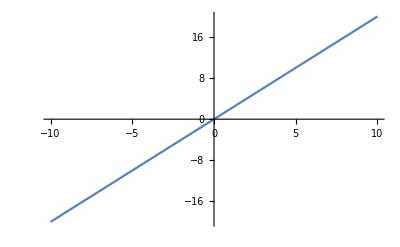
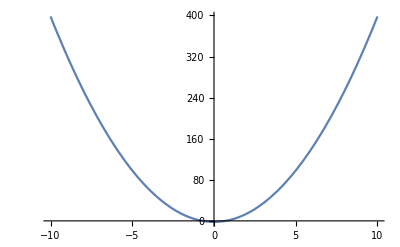
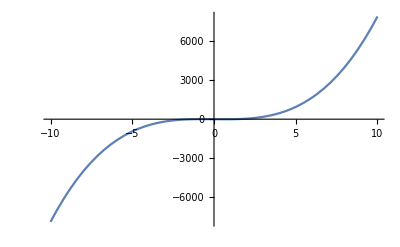
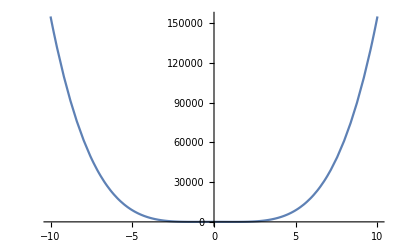
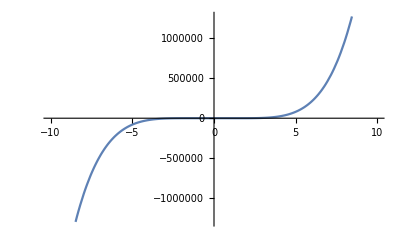
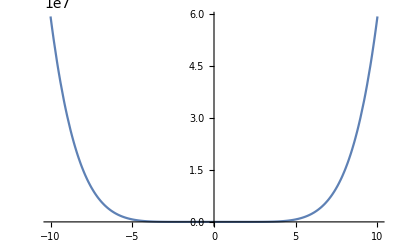
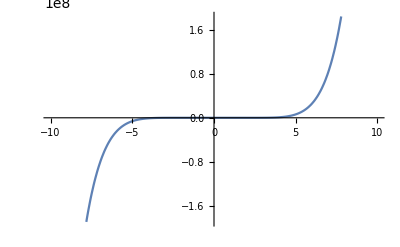
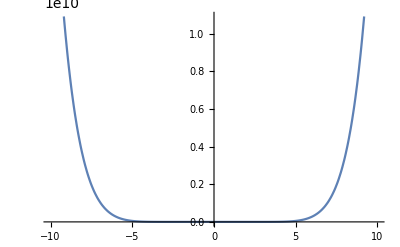

```mathematica
Table[Plot[HermiteH[n,xi],{xi,-10,10}],{n,1,10}]
```

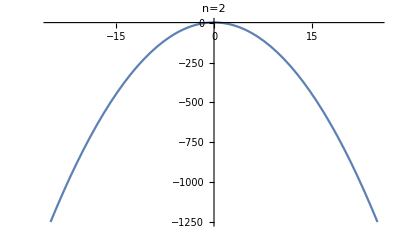
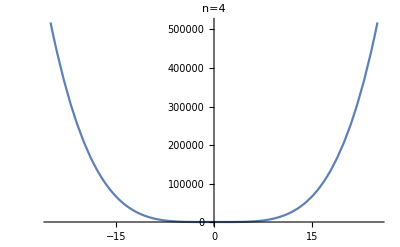
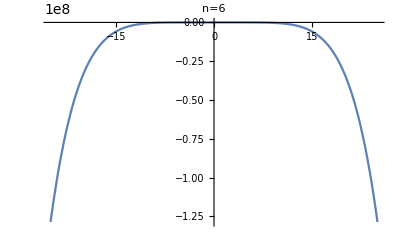
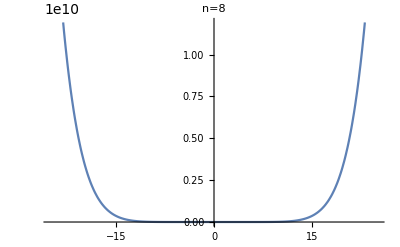
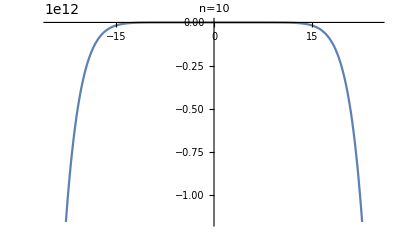
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[Hypergeometric1F1[-(n/2),1/2,xi^2],{xi,-25,25},AxesLabel->StringForm[ "n=``",n," "]],{n,1,10}]
```

```mathematica
(* ΕΛΕΓΧΟΥΜΕ ΑΝ ΥΠΑΡΧΕΙ ΓΡΑΜΙΚΗ ΣΧΕΣΗ ΜΕΤΑΞΥ ΤΩΝ ΔΙΑΦΟΡΩΝ ΛΥΣΕΩΝ *)
(* ΟΠΩΣ ΑΝΑΜΕΝΕΤΑΙ ΓΙΑ n=2k ΟΙ ΛΥΣΕΙΣ ΕΙΝΑΙ ΓΡΑΜΙΚΑ ΕΞΑΡΤΗΜΕΝΕΣ ΕΝΩ ΓΙΑ n=2k+1 ΔΕΝ ΕΙΝΑΙ *)
```

```mathematica
Do[herm1overherm2=Simplify[(herm1E2nPlus1[xi]/herm2E2nPlus1[xi] )/.n->i ]//PowerExpand;
Print["herm1overherm2[n=",i,"]=", herm1overherm2],
{i,0,10}]
```

herm1overherm2[n=0]=1

herm1overherm2[n=1]=(2 xi^2)/(ⅇ^(xi^2) xi-√π xi^2 Erfi[xi])

herm1overherm2[n=2]=-2

herm1overherm2[n=3]=-(8 xi^2 (-3+2 xi^2))/(2 ⅇ^(xi^2) xi (-1+xi^2)+√π xi^2 (3-2 xi^2) Erfi[xi])

herm1overherm2[n=4]=12

herm1overherm2[n=5]=(64 xi^2 (15-20 xi^2+4 xi^4))/(2 ⅇ^(xi^2) xi (4-9 xi^2+2 xi^4)+√π xi^2 (-15+20 xi^2-4 xi^4) Erfi[xi])

herm1overherm2[n=6]=-120

herm1overherm2[n=7]=-(768 xi^2 (-105+210 xi^2-84 xi^4+8 xi^6))/(2 ⅇ^(xi^2) xi (-24+87 xi^2-40 xi^4+4 xi^6)+√π xi^2 (105-210 xi^2+84 xi^4-8 xi^6) Erfi[xi])

herm1overherm2[n=8]=1680

herm1overherm2[n=9]=(12288 xi^2 (945-2520 xi^2+1512 xi^4-288 xi^6+16 xi^8))/(2 ⅇ^(xi^2) xi (192-975 xi^2+690 xi^4-140 xi^6+8 xi^8)+√π xi^2 (-945+2520 xi^2-1512 xi^4+288 xi^6-16 xi^8) Erfi[xi])

herm1overherm2[n=10]=-30240